## UndangleVertices-example.nb UndangleVertices, UndangleEdges example

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51i (18 June 2017)) loaded Sun 18 Jun 2017 11:15:31
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

Create a tissue with a point and an edge that aren't used.

```mathematica
v={{0,0}, {2, 0}, {1, 2}, {2, 1}, {2, 2}};
e={{1,2},  {2, 3}, {3, 1}, {3, 4}}; 
c={{1,2,3}}; 
q=Tissue[v,e,c]
```

Tissue[{{0,0},{2,0},{1,2},{2,1},{2,2}},{{1,2},{2,3},{3,1},{3,4}},{{1,2,3}}]

```mathematica
DanglingEdges[q]
```

{4}

```mathematica
DanglingVertices[q]|
```

{5}

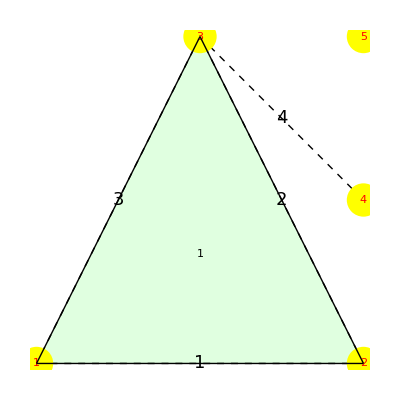

```mathematica
ShowTissue[q, "Vertices"-> {Yellow, PointSize[.06]}, "VertexNumbers"->{Red, FontSize-> 20}, "CellNumbers"-> True , "EdgeNumbers"-> True, "EdgeNumberStyle"-> {Black, FontSize-> 18}, "All"-> True , "EdgeStyles"-> Dashed]
```

## Undangling Vertices removes vertex 5 which is not attached to anything

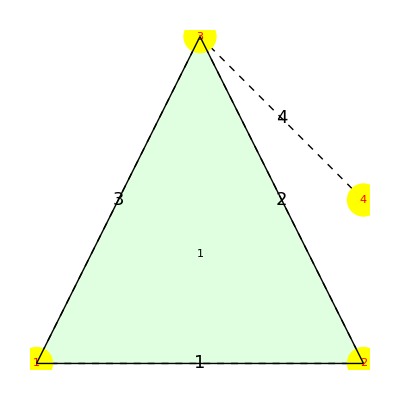

```mathematica
ShowTissue[UndangleVertices[q],"Vertices"-> {Yellow, PointSize[.06]}, "VertexNumbers"->{Red, FontSize-> 20}, "CellNumbers"-> True , "EdgeNumbers"-> True, "EdgeNumberStyle"-> {Black, FontSize-> 18}, "All"-> True , "EdgeStyles"-> Dashed]
```

## Undangle edge removes edge 4 which is not attached to anything, but the dangling vertices are still there

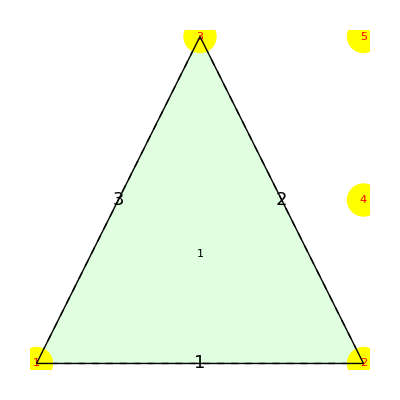

```mathematica
ShowTissue[UndangleEdges[q],"Vertices"-> {Yellow, PointSize[.06]}, "VertexNumbers"->{Red, FontSize-> 20}, "CellNumbers"-> True , "EdgeNumbers"-> True, "EdgeNumberStyle"-> {Black, FontSize-> 18}, "All"-> True , "EdgeStyles"-> Dashed]
```

## Undangling Vertices after Undangling edges takes care of all the extra stuff

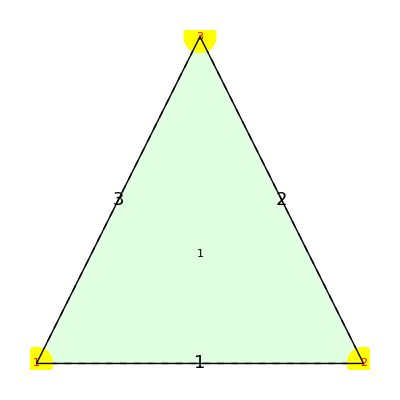

```mathematica
ShowTissue[UndangleVertices[UndangleEdges[q]], "Vertices"-> {Yellow, PointSize[.06]}, "VertexNumbers"->{Red, FontSize-> 20}, "CellNumbers"-> True , "EdgeNumbers"-> True, "EdgeNumberStyle"-> {Black, FontSize-> 18}, "All"-> True , "EdgeStyles"-> Dashed]
```